## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

## From Giulio regarding parsing:

```mathematica
ClearAll[parseInput,takepart]
```

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]
```

```mathematica
good="f[1,g[1,2],3]";
```

```mathematica
bad="f[1,g[1,2,3]";
```

```mathematica
correction1="f[1,g[1,2,3]]";
```

```mathematica
correction2="f[1,g[1,2],3]";
```

```mathematica
Replace[Level[parseInput["Exp[1+2Sin[x]]"],{3}],x_/;!AtomQ[x]:>Head[x],{1}]
```

```mathematica
Replace[Level[parseInput["Exp[1+2Sin[x]]"],{4}],x_/;!AtomQ[x]:>Head[x],{1}][[1]]
```

Sin

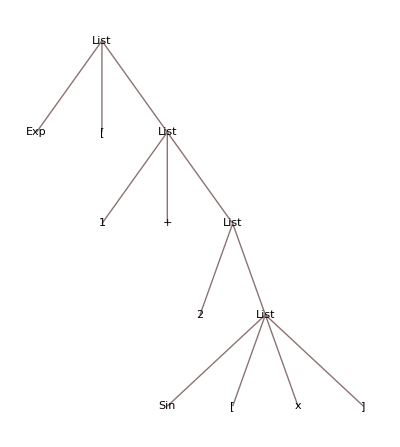

```mathematica
myexpression= parseInput@"Exp[1+2Sin[x]";myexpression//TreeForm
```

```mathematica
getlevels[n_Integer]:=With[{el=n},Replace[Level[myexpression,{el}],x_/;!AtomQ[x]:>ToString[Head[x]],{1}]]
```

```mathematica
(* I hardcoded the number 4 here *)
```

```mathematica
alllevels=Thread[getlevels[Range[4]]];alllevels//Column
```

{Exp,[,List}
{1,+,List}
{2,List}
{Sin,[,x,]}

```mathematica
Depth[myexpression]
```

5

```mathematica
Thread[Head[alllevels]]
```

List

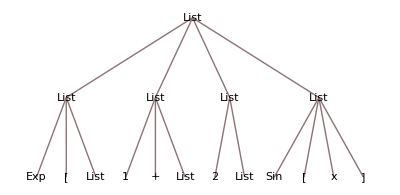

```mathematica
alllevels//TreeForm
```

```mathematica
Thread[StringCount[alllevels,"["]]
```

StringCount::strse: String or list of strings expected at position 1 in StringCount[{{Exp,[,List},{1,+,List},{2,List},{Sin,[,x,]}},[].

{{0,1,0},{0,0,0},{0,0},{0,1,0,0}}

```mathematica
listA=Total/@Table[StringCount[alllevels[[i]],"["],{i,Length[alllevels]}];
```

```mathematica
Map[StringCount[#,"["]&,alllevels,{2}]
```

{{0,1,0},{0,0,0},{0,0},{0,1,0,0}}

```mathematica
listB=Total/@Table[StringCount[alllevels[[i]],"]"],{i,Length[alllevels]}]
```

{0,0,0,1}

```mathematica
Map[Table[StringCount[alllevels[[i]],"["],{i,Length[alllevels]}],Table[StringCount[alllevels[[i]],"]"],{i,Length[alllevels]}]]//TraditionalForm
```

```mathematica
Print["Function ",  getlevels[Position[MapThread[Equal,{listA,listB}] ,False][[1,1]]]," is missing a bracket"]
```

Function {Exp,[,List} is missing a bracket

```mathematica
getlevels[1]
```

{Exp,[,List}